```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 175 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,Parallel`Debug`Perfmon`,Parallel`Debug`,System`,Global`}

```mathematica
(* Leaving out the first part of the derivation *)
```

```mathematica
Clear[ℒ]
ℒ = 1/2 m a^2 θ'[t]^2 + 1/2 m a ω^2 Sin[θ[t]]^2 + m g a Cos[θ[t]]
```

a g m Cos[θ[t]]+1/2 a m ω^2 Sin[θ[t]]^2+1/2 a^2 m θ'[t]^2

```mathematica
Clear[q]
q = θ[t]
```

θ[t]

```mathematica
D[ D[ ℒ , D[q, t] ] ,t ]  - D[ ℒ , q ] // Simplify
```

a m ((g-ω^2 Cos[θ[t]]) Sin[θ[t]]+a θ''[t])

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t ] ;
eqs // pdConv
```

-a m (a (∂^2 θ(t))/(∂t^2)+sin(θ(t)) (g-ω^2 cos(θ(t))))==0

```mathematica
Clear[com]
com = 
FirstIntegrals[ ℒ , q, t ]  ;
com // pdConv
```

{FirstIntegral(t)→1/2 a m (a ((∂θ(t))/(∂t))^2-2 g cos(θ(t))-ω^2 sin^2(θ(t)))}

```mathematica
D[q, t] D[ ℒ , D[q, t] ] - ℒ  // Simplify
```

1/2 a m (-2 g Cos[θ[t]]-ω^2 Sin[θ[t]]^2+a θ'[t]^2)

```mathematica
eqs 
eqs /. θ''[t]-> 0
```

-a m ((g-ω^2 Cos[θ[t]]) Sin[θ[t]]+a θ''[t])==0

-a m (g-ω^2 Cos[θ[t]]) Sin[θ[t]]==0

```mathematica
Clear[equilibrium]
equilibrium = 
eqs /. θ''[t]-> 0
```

-a m (g-ω^2 Cos[θ[t]]) Sin[θ[t]]==0

```mathematica
equilibrium[[1,4]]
equilibrium[[1,5]]
```

g-ω^2 Cos[θ[t]]

Sin[θ[t]]

```mathematica
Solve[equilibrium[[1,4]] ==  0 , θ[t] ]  /. C[1]-> 0
```

{{θ[t]→-ArcCos[g/ω^2]},{θ[t]→ArcCos[g/ω^2]}}

```mathematica
Solve[equilibrium[[1,5]] == 0 , θ[t] ] /. C[1]-> 0
```

{{θ[t]→0},{θ[t]→π}}

```mathematica
Clear[θTransform]
θTransform = 
θ[t] == θ0 + α[t]
```

θ[t]==θ0+α[t]

```mathematica
Flatten[Solve[ θTransform , θ[t] ]] 
Flatten[Solve[ θTransform , α[t] ]]
```

{θ[t]→θ0+α[t]}

{α[t]→-θ0+θ[t]}

```mathematica
Clear[θReplace]
θReplace = 
Flatten[Solve[ θTransform , θ[t] ]]
```

{θ[t]→θ0+α[t]}

```mathematica
D[θReplace, t]
```

{θ'[t]→α'[t]}

```mathematica
D[D[θReplace, t], t]
```

{θ''[t]→α''[t]}

```mathematica
eqs
eqs /. θReplace 
eqs /. θReplace  /. D[D[θReplace, t], t]
```

-a m ((g-ω^2 Cos[θ[t]]) Sin[θ[t]]+a θ''[t])==0

-a m ((g-ω^2 Cos[θ0+α[t]]) Sin[θ0+α[t]]+a θ''[t])==0

-a m ((g-ω^2 Cos[θ0+α[t]]) Sin[θ0+α[t]]+a α''[t])==0

```mathematica
eqs /. θReplace  /. D[D[θReplace, t], t]  // Simplify
```

a m ((g-ω^2 Cos[θ0+α[t]]) Sin[θ0+α[t]]+a α''[t])==0

```mathematica
(* 
Sin[ θ0 + α[t]] // TrigExpand 
Cos[α[t]] Sin[θ0]+Cos[θ0] Sin[α[t]]
Sin[ θ0 + α[t]]  // TrigExpand 
Cos[α[t]] Sin[θ0]+Cos[θ0] Sin[α[t]]
Cos[α[t]]-> 1 ,
Sin[α[t]]-> α[t]
eqs /. θReplace  /. ∂_t ∂_t θReplace  // TrigExpand  //.  Cos[α[t]]-> 1  //.  Sin[α[t]]-> α[t] 
-a g m Cos[α[t]] Sin[θ0]+a m ω^2 Cos[θ0] Cos[α[t]]^2 Sin[θ0]-a g m Cos[θ0] Sin[α[t]]+a m ω^2 Cos[θ0]^2 Cos[α[t]] Sin[α[t]]-a m ω^2 Cos[α[t]] Sin[θ0]^2 Sin[α[t]]-a m ω^2 Cos[θ0] Sin[θ0] Sin[α[t]]^2-a^2 m α''[t]==0
*)

(* 
This was a futile exercise 
*)
```

```mathematica
(* This works, I can't believe it *) 
Clear[eqc]
eqc = 
Normal[Series[ eqs/. θReplace  /. D[D[θReplace, t], t]   , {  α[t] , 0, 1 } ]]   // Expand // Simplify
```

a m ((g-ω^2 Cos[θ0]) Sin[θ0]+(g Cos[θ0]-ω^2 Cos[2 θ0]) α[t]+a α''[t])==0

```mathematica
θTransform
D[θTransform, t]
D[D[θTransform, t], t]
```

θ[t]==θ0+α[t]

θ'[t]==α'[t]

θ''[t]==α''[t]

```mathematica
Flatten[Solve[ D[D[θTransform, t], t] /. θ''[t]-> 0 , α''[t]]]
```

{α''[t]→0}

```mathematica
eqc /. Flatten[Solve[ D[D[θTransform, t], t] /. θ''[t]-> 0 , α''[t]]]
```

a m ((g-ω^2 Cos[θ0]) Sin[θ0]+(g Cos[θ0]-ω^2 Cos[2 θ0]) α[t])==0

```mathematica
eqs
```

-a m ((g-ω^2 Cos[θ[t]]) Sin[θ[t]]+a θ''[t])==0

```mathematica
Clear[parameters]
parameters = {
m-> 20 , 
g-> 9.8 , 
ω-> 0.2  , 
a-> 0.5 
} ;
parameters // TableForm
```

m→20
g→9.8
ω→0.2
a→0.5

```mathematica
eqs /. parameters  // Expand
```

-98. Sin[θ[t]]+0.4 Cos[θ[t]] Sin[θ[t]]-5. θ''[t]==0

```mathematica
Clear[ics]
ics = { 
θ[0] == 0.1 , 
θ'[0] == 0.1 
} ;
```

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ { eqs } /. parameters , ics ] , q , { t, 0, 10 } ] ]
```

{θ[t]→InterpolatingFunction[…][t]}

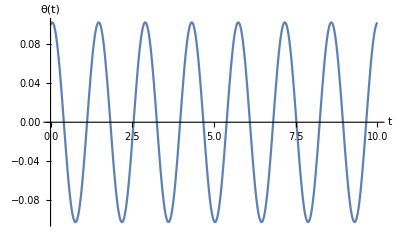

```mathematica
Plot[ Evaluate[ q /. solution[t]]  ,  { t, 0, 10 }, AxesLabel-> { t, q }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q , D[q, t] } ]  ,
{ tmax , 1 ,10 , 0.5  } ]
```